# The Sandpile Model

Jonas Kaufman & Jon Ueki
May 4, 2016

## The Bak-Tang-Wiesenfeld Model

Cellular automaton to model “spatially extended dynamical systems”

Displays self-organizing critical behavior, 1/f noise

Not just sand: earthquakes, human brain, Congress

-Graphics-

http://www.wisegeek.org/what-is-silica-sand.htm

## 1-D Model Rules

Row of N cells representing half a sandpile

Each cell has height h_i and slope z_i where z_i=h_i-h_(i+1)

Adding a grain at cell i:

z_i → z_i+1

z_(i-1) → z_(i-1)-1

If z_i > z_c, cell “topples,” sending one grain of sand to the next cell down:

z_i  → z_i- 2

z_(i±1) → z_(i±1) + 1

Left boundary is closed, right boundary is open

## 1-D Model Rules

-Graphics-

http://link.aps.org/doi/10.1103/PhysRevA.38.364

## 1-D Model in Action

N = 20, z_c=1, z_i=0 initially

Grains added randomly, pile relaxes between grains

Reaches stable state z_i = z_c

```mathematica
length=10;
zCrit1D=1;

constantRow[c_]:=row=Table[c,{length}]

addGrain[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];

relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit1D,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]

pourSand[numGrains_]:=Module[{n,rows={row}},
For[n=1,n≤numGrains,n++,
addGrain[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]

constantRow[0];
rows=pourSand[150];
Animate[GraphicsRow[{
ListStepPlot[rows[[t]],AxesLabel->{"i","z"},PlotRange->{-zCrit1D-1,zCrit1D+1},LabelStyle->Large],
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],AxesLabel->{"i","h"},PlotRange->{0,length*zCrit1D+1},LabelStyle->Large]
},ImageSize->Large,AspectRatio->3/4],
{t,1,Length[rows],1,Appearance->"Labeled"},LabelStyle->Medium,AnimationRunning->False,AnimationRate->Automatic]
```

## 2-D Model Rules

N x N grid representing a quarter sandpile

“Slope” is z_(i,j)=2 h_(i,j)-h_(i+1,j)-h_(i,j+1)

Adding a grain at z_(i,j):

z_(i,j) → z_(i,j)+2

z_(i-1,j) → z_(i-1,j)-1, z_(i,j-1) → z_(i,j-1)-1

Toppling:

z_(i,j) → z_(i,j)-4

z_(i±1,j) → z_(i±1,j)+1, z_(i,j±1) → z_(i,j±1)+1

## Dropping Sand in One Spot vs Randomly

Drop Sand in Center of Pile		Drop Sand Randomly
-Graphics3D- 		 -Graphics3D-

Dropping

## Frequency of an Avalanche of a certain size

Drop Sand in Center		      Drop Sand Randomly

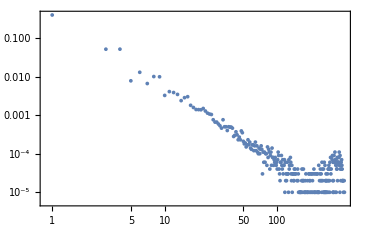
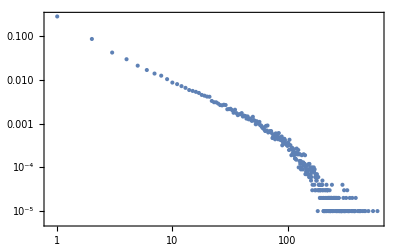

Randomly dropped sand gives larger and Avalanches

Centerly dropped sand has more larger avalanches than medium ones

## Slope Statistics

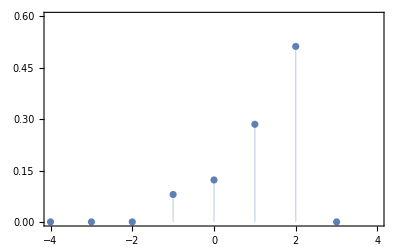
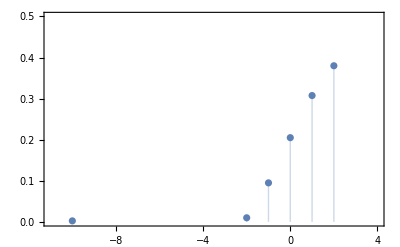

## Super Critical Sandpile

Start the sandpile in an unstable stable (Zi = 9, where Zc=3)

-Graphics3D-

Let the sandpile relax into a minimally critical state

-Graphics3D-

Perturb by dropping 100k grains of sand

-Graphics3D-

## Different Initial Conditions - Same Critical State

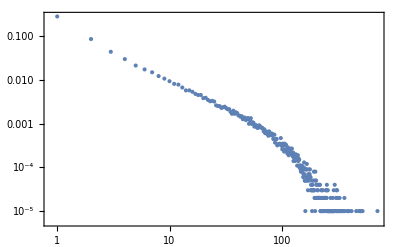
-Graphics-	-Graphics-

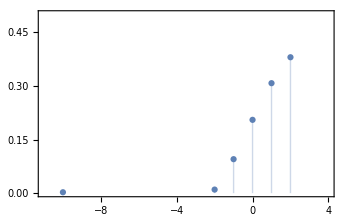
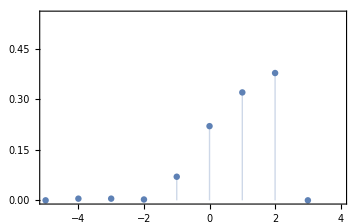

## Conclusion

Model reaches critical state under different initial conditions

Distribution of avalanche sizes follows a 1/f power law

Future directions:

More avalanche statistics

Different boundary conditions

Different lattice geometry

Higher dimensions